# Coupled Oscillations and Normal Modes

## Juan Jose Neri

### Problem 11.7

-Graphics-

```mathematica
x1[t_]:=(B1 Cos[w1 t]+C1 Sin[w1 t])+(B2 Cos[w2 t]+C2 Sin[w2 t]);
x2[t_]:=(B1 Cos[w1 t]+C1 Sin[w1 t])-(B2 Cos[w2 t]+C2 Sin[w2 t]);
v1[t_]:=x1'[t];
v2[t_]:=x2'[t];
```

#### Get the initial conditions

```mathematica
{x1[0],x2[0],v1[0],v2[0]}
```

{B1+B2,B1-B2,C1 w1+C2 w2,C1 w1-C2 w2}

#### Find the coefficients

```mathematica
Solve[{x1[0]==A,x2[0]==A,v1[0]==0,v2[0]==0},{B1,B2,C1,C2}]
```

{{B1→A,B2→0,C1→0,C2→0}}

#### The original equations become

```mathematica
x1[t_]:=A Cos[w1 t];
x2[t_]:=A Cos[w1 t];
```

#### Take A and w1 to be 1

```mathematica
x1[t_]:=Cos[t];
x2[t_]:=Cos[t];
```

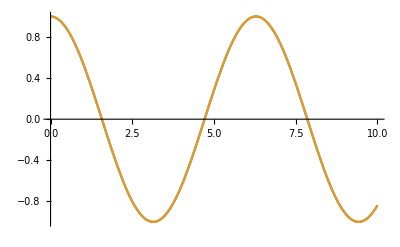

```mathematica
Plot[{x1[t],x2[t]},{t,0,10}]
```

```mathematica
x1[t_]:=(B1 Cos[w1 t]+C1 Sin[w1 t])+(B2 Cos[w2 t]+C2 Sin[w2 t]);
x2[t_]:=(B1 Cos[w1 t]+C1 Sin[w1 t])-(B2 Cos[w2 t]+C2 Sin[w2 t]);
v1[t_]:=x1'[t];
v2[t_]:=x2'[t];
```

#### Get the initial conditions

```mathematica
{x1[0],x2[0],v1[0],v2[0]}
```

{B1+B2,B1-B2,C1 w1+C2 w2,C1 w1-C2 w2}

#### Find the coefficients

```mathematica
Solve[{x1[0]==A,x2[0]==0,v1[0]==0,v2[0]==0},{B1,B2,C1,C2}]
```

{{B1→A/2,B2→A/2,C1→0,C2→0}}

#### The original equations become

```mathematica
x1[t_]:=A/2 (Cos[w1 t]+Cos[w2 t]);
x2[t_]:=A/2 (Cos[w1 t]-Cos[w2 t]);
```

#### Take A, w1 to be 1 and w2 to be √3

```mathematica
x1[t_]:=1/2 (Cos[t]+Cos[√3 t]);
x2[t_]:=1/2( Cos[ t]-Cos[√3 t]);
```

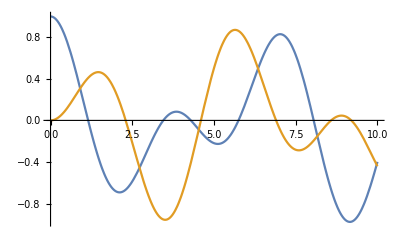

```mathematica
Plot[{x1[t],x2[t]},{t,0,10}]
```